```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
eqs=<<eqs.m;
eqsz0=<<eqsz0.m;
eqsz1=<<eqsz1.m;
eqsxb=<<eqsxb.m;
jacobi=<<jacobi.m;
jacobiz0=<<jacobiz0.m;
jacobiz1=<<jacobiz1.m;
jacobixb=<<jacobixb.m;
eqs//MatrixForm
jacobi//MatrixForm
```

(Q6[z,x] (-z+Q7[z,x]^2/(1-z^3))+Q6^(0,2)[z,x]-3 z^2 Q6^(1,0)[z,x]+(1-z^3) Q6^(2,0)[z,x]
-Q6[z,x]^2 Q7[z,x]+Q7^(0,2)[z,x]+(1-z^3) Q7^(2,0)[z,x])

(eye (-z-Q7[z,x]^2/(-1+z^3))+d_(0,2)-3 z^2 d_(1,0)+(1-z^3) d_(2,0) | -(2 eye Q6[z,x] Q7[z,x])/(-1+z^3)
-2 eye Q6[z,x] Q7[z,x] | -eye Q6[z,x]^2+d_(0,2)+(1-z^3) d_(2,0))

```mathematica
mu=5.6;Lz=1;Lx=20.0;cuttoff=1.-10.^-9;
Nz=20;Nx=20;Nzx=Nz*Nx;
Eye=IdentityMatrix[Nzx];Zero=ConstantArray[0,{Nzx,Nzx}];
cgl[n_]:=Table[Cos[(i π)/(n-1.0)],{i,n-1,0,-1}];
gridz=0.5(cgl[Nz]+1);
gridx=0.5Lx cgl[Nx];
zz=gridz⊗ConstantArray[1,Nx];Z=Flatten[zz];
xx=ConstantArray[1,Nz]⊗gridx;X=Flatten[xx];
z0=Flatten[Position[Z,n_/;n==gridz⟦1⟧]];
z1=Flatten[Position[Z,n_/;n==gridz⟦-1⟧]];
xb=Flatten[Position[X,n_/;(n==gridx⟦1⟧|| n==gridx⟦-1⟧)]];
Z⟦z1⟧=cuttoff;(*在Horizon取小的截断以免离散化方程出现发散项*)
(*谱求导矩阵生成函数*)
(*cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,n}];sdm=2/l Table[If[i≠j,c⟦i⟧/c⟦j⟧(-1)^(i+j)/(x⟦i⟧-x⟦j⟧),0],{i,n},{j,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];*)
(*内置chebyshev微分矩阵*)
dz1=NDSolve`FiniteDifferenceDerivative[1,gridz,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix"//Normal;
dz2=NDSolve`FiniteDifferenceDerivative[2,gridz,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix"//Normal;
dx1=NDSolve`FiniteDifferenceDerivative[1,gridx,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix"//Normal;
dx2=NDSolve`FiniteDifferenceDerivative[2,gridx,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix"//Normal;
dzs[0]=IdentityMatrix[Nz];dzs[1]=dz1;dzs[2]=dz2;
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx1;dxs[2]=dx2;
Do[If[i+j≤2,ds[i,j]=KroneckerProduct[dzs[i],dxs[j]]],{i,0,2},{j,0,2}];
(*在CGL格点上，二阶有限差分求导矩阵*)
fdz1=NDSolve`FiniteDifferenceDerivative[1,gridz,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal;
fdz2=NDSolve`FiniteDifferenceDerivative[2,gridz,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal;
fdx1=NDSolve`FiniteDifferenceDerivative[1,gridx,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal;
fdx2=NDSolve`FiniteDifferenceDerivative[2,gridx,"DifferenceOrder"->2]@"DifferentiationMatrix"//Normal;
fdzs[0]=IdentityMatrix[Nz];fdzs[1]=fdz1;fdzs[2]=fdz2;
fdxs[0]=IdentityMatrix[Nx];fdxs[1]=fdx1;fdxs[2]=fdx2;
Do[If[i+j≤2,fds[i,j]=KroneckerProduct[fdzs[i],fdxs[j]]],{i,0,2},{j,0,2}];
```

### centered finite difference

```mathematica
hz=Table[gridz⟦j+1⟧-gridz⟦j⟧,{j,1,Nz-1}];
hx=Table[gridx⟦j+1⟧-gridz⟦j⟧,{j,1,Nx-1}];
```

## Newton-Kantorovich Method

```mathematica
(*Initializaton*)
q6=s[Q6]=4Z Tanh[X];
q7=s[Q7]=mu(1-Z) ;
(*q6=s[Q6]=<<Q6last.m;
q7=s[Q7]=<<Q7last.m;*)
seed=Join[q6,q7];sol=seed;length=Length[seed];
(*EYE=IdentityMatrix[length]//SparseArray;*)
eps=10.^-6;tol=10.^-6;k=0;kmax=16;τ=0.2;
Monitor[While[k<kmax,
diseqs=eqs/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
diseqsz0=eqsz0/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z0⟧).s[h],h_[z,x]:>s[h]⟦z0⟧};
diseqsz1=eqsz1/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z1⟧).s[h],h_[z,x]:>s[h]⟦z1⟧};
diseqsxb=eqsxb/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦xb⟧).s[h],h_[z,x]:>s[h]⟦xb⟧};
diseqs⟦;;,z0⟧=diseqsz0;
diseqs⟦;;,z1⟧=diseqsz1;
diseqs⟦;;,xb⟧=diseqsxb;
b=-Flatten[diseqs];
J=jacobi/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],Subscript[d, i_,j_]->ds[i,j],eye->Eye,zero->Zero,z->Z};
Jz0=jacobiz0/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z0⟧).s[h],h_[z,x]:> s[h]⟦z0⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z0⟧,eye:> Eye⟦z0⟧,zero:> Zero⟦z0⟧};
Jz1=jacobiz1/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z1⟧).s[h],h_[z,x]:> s[h]⟦z1⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z1⟧,eye:> Eye⟦z1⟧,zero:> Zero⟦z1⟧};
Jxb=jacobixb/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦xb⟧).s[h],h_[z,x]:> s[h]⟦xb⟧,Subscript[d, i_,j_]:> ds[i,j]⟦xb⟧,eye:> Eye⟦xb⟧,zero:> Zero⟦xb⟧};
J⟦;;,;;,z0⟧=Jz0;
J⟦;;,;;,z1⟧=Jz1;
J⟦;;,;;,xb⟧=Jxb;
J=ArrayFlatten[J];
(*二阶有限差分雅可比*)
fJ=jacobi/.{Derivative[i_,j_][h_][z,x]->fds[i,j].s[h],h_[z,x]->s[h],Subscript[d, i_,j_]->fds[i,j],eye->Eye,zero->Zero,z->Z};
fJz0=jacobiz0/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦z0⟧).s[h],h_[z,x]:> s[h]⟦z0⟧,Subscript[d, i_,j_]:> fds[i,j]⟦z0⟧,eye:> Eye⟦z0⟧,zero:> Zero⟦z0⟧};
fJz1=jacobiz1/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦z1⟧).s[h],h_[z,x]:> s[h]⟦z1⟧,Subscript[d, i_,j_]:> fds[i,j]⟦z1⟧,eye:> Eye⟦z1⟧,zero:> Zero⟦z1⟧};
fJxb=jacobixb/.{Derivative[i_,j_][h_][z,x]:> (fds[i,j]⟦xb⟧).s[h],h_[z,x]:> s[h]⟦xb⟧,Subscript[d, i_,j_]:> fds[i,j]⟦xb⟧,eye:> Eye⟦xb⟧,zero:> Zero⟦xb⟧};
fJ⟦;;,;;,z0⟧=fJz0;
fJ⟦;;,;;,z1⟧=fJz1;
fJ⟦;;,;;,xb⟧=fJxb;
fJ=ArrayFlatten[fJ]//SparseArray;
Jb=Append[Jᵀ,b]ᵀ;
preJb=LinearSolve[fJ,Jb,Method->"Pardiso"];(*preconditioner*)
Label["Richardson_Iteration"];
soln=sol-τ(preJb⟦;;,1;;-2⟧.sol-preJb⟦;;,-1⟧);
tolrms=√(Total[(soln-sol)^2]/length);
If[tolrms>tol,If[tolrms<10,sol=soln;Goto["Richardson_Iteration"],Print["Failed"];Break[]]];
(*sol=LinearSolve[J,b];*)(*direct method*)
seed=seed+sol;
reseed=ArrayReshape[seed,{2,Nzx}];
q6=s[Q6]=reseed⟦1⟧;
q7=s[Q7]=reseed⟦2⟧;
solrms=√(Total[sol^2]/length);brms=√(Total[b^2]/length);
If[solrms<eps,Break[],k++];
],{tolrms,solrms,brms}]//Timing
```

Failed

{33.625,Null}

-Graphics3D-

-Graphics3D-

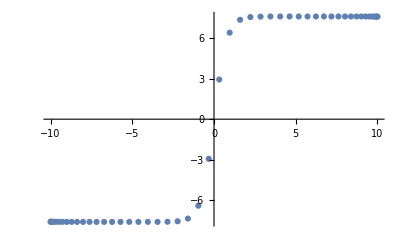

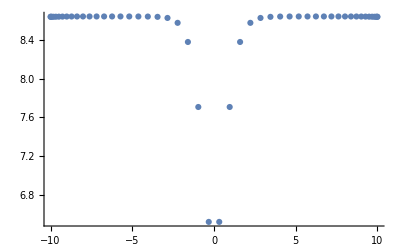

```mathematica
solq6=ArrayReshape[q6,{Nz,Nx}];
solq7=ArrayReshape[q7,{Nz,Nx}];
orderp=dz1⟦1⟧.solq6;
rho=-(dz1⟦1⟧.solq7);
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq6⟦i,j⟧},{i,Nz},{j,Nx}],1]]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq7⟦i,j⟧},{i,Nz},{j,Nx}],1]]
ListPlot[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,Nx}],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,rho⟦i⟧},{i,Nx}],PlotRange->All]
```